# Server connect

```mathematica
CloseKernels[]
```

{}

```mathematica
kernel=KernelConfiguration["ssh://strelda@ipnp36.troja.mff.cuni.cz"];
```

```mathematica
LaunchKernels[kernel,16]
```

{strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz,strelda@ipnp36.troja.mff.cuni.cz}

```mathematica
$PlotTheme="Scientific";
```

# Functions

## Model definition

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
Jx[n_?IntegerQ]:=Module[{diag,b1,b2,m},
b1=Je[1,n/2,m]/2;(*1. offdiagonal*)

SparseArray[{
Band[{1,2},{n,n+1}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1*,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*)
},{n+1,n+1}]
]
Jy[n_?IntegerQ]:=Module[{diag,b1,b2,m},
b1=Je[1,n/2,m]/(2I) ;(*1. offdiagonal*)
SparseArray[{
Band[{1,2},{n,n+1}]->Table[b1,{m,n/2-1,-n/2,-1}] (*1. upper offdiagonal*),
Band[{2,1},{n+1,n}]->Table[b1*,{m,n/2-1,-n/2,-1}] (*1. lower offdiagonal*)
},{n+1,n+1}]
]
Jz[n_?IntegerQ]:=Module[{diag,b1,b2,m},
diag=m;(*diagonal*)

SparseArray[{
Band[{1,1},{n+1,n+1}]->Table[diag,{m,n/2,-n/2,-1}](*diagonal*)
},{n+1,n+1}]
]
```

```mathematica
H0[n_?IntegerQ,α_]:=α Jx[n]
Hz[n_?IntegerQ,κ_]:=κ/(2n/2)Jz[n].Jz[n]
```

```mathematica
Floq[n_?IntegerQ,α_,κ_]:=MatrixExp[-I Hz[n,κ]].MatrixExp[-I H0[n,α]]
```

## Multifract something

```mathematica
CohState[n_,{θ_,ϕ_}]:=Module[{j,ζ},
(*Coherent state  at dimension n*)
j=n/2;
ζ=Tan[θ/2]Exp[I ϕ];
Table[ζ^(j-m)/((1+Abs[ζ]^2)^j)√(((2j)!)/((j+m)!(j-m)!)),{m,j,-j,-1}]
]
```

```mathematica
MultifractTabGenerator[operator_,q_,res_]:=Module[{eigs,eigv,n,c,Multifract,MultifractC,mult},
{eigs,eigv}=Eigensystem[operator];

n=Length[eigs]-1;
c[θ_?NumericQ,ϕ_?NumericQ]:=Map[(N@CohState[n,{θ,ϕ}]*.#)&,eigv];

Multifract[θ_?NumericQ,ϕ_?NumericQ]:=1./Log[1.+n] 1./(1.-q)Log[Total[Abs[c[θ,ϕ]]^(2q)]];
Flatten[ParallelTable[{ϕ,θ,Quiet[Multifract[θ,ϕ]/.Indeterminate->0]},{ϕ,-N@π,N@π,2π/res},{θ,10^-3,N@π,π/res}],1]
]
```

```mathematica
MultifractTabGeneratork[operator_,q_,res_,k_]:=Module[{eigs,eigv,eigsN,eigvN,n,c,Multifract,MultifractC,mult,overlap,trajectory},
{eigsN,eigvN}=Eigensystem[operator];
{eigs,eigv}=Transpose@SortBy[Transpose[{eigsN,eigvN}],(ArcCos@Re[First[#]])&];

n=Length[eigs]-1;
c[kk_,θ_?NumericQ,ϕ_?NumericQ]:=N@CohState[n,{θ,ϕ}]*.eigv[[kk]];

(*Multifract[kk_,θ_?NumericQ,ϕ_?NumericQ]:=1./Log[1.+n] 1./(1.-q)Log[Abs[c[k,θ,ϕ]]^(2q)];
overlap=NIntegrate[Multifract[k,θ,ϕ],{θ,0,π},{ϕ,-π,π}];*)
trajectory=Flatten[Table[{ϕ,θ,Quiet@(Abs[c[k,θ,ϕ]]^(2q))/.Indeterminate->0},{ϕ,-N@π,N@π,2π/res},{θ,10^-3,N@π,π/res}],1];

trajectory
]
```

```mathematica
MultifractTabGeneratorOverlapK[operator_,q_,k_]:=Module[{eigs,eigv,eigsN,eigvN,n,c,Multifract,MultifractC,mult,overlap,trajectory},
{eigsN,eigvN}=Eigensystem[operator];
{eigs,eigv}=Transpose@SortBy[Transpose[{eigsN,eigvN}],Re[First[#]]&];

n=Length[eigs]-1;
c[kk_,θ_?NumericQ,ϕ_?NumericQ]:=N@CohState[n,{θ,ϕ}]*.eigv[[kk]];

Multifract[kk_,θ_?NumericQ,ϕ_?NumericQ]:=Abs[c[kk,θ,ϕ]]^(2q);
NIntegrate[Multifract[k,θ,ϕ],{θ,0,π},{ϕ,-π,π}]
]
```

# BCH

## BCH formula based on https://arxiv.org/pdf/0810.2656.pdf

```mathematica
<<"/Users/strelda/Library/Mobile Documents/com~apple~CloudDocs/Files/synced Documents/phd/lukas/bch_and_chaos/NonCommutativeMultiply.wl"
```

```mathematica
(*Error Handling*)
highorder::highorder="Order has to be less than 111013";
checkOrder[order_Integer]:=If[order>=111013,Message[highorder::highorder];Abort[]];
```

```mathematica
(*They offer a formula for obtaining these coefficients, but for now this talbe generated by the authors is sufficient.*)
coeffDataOriginal=Import[NotebookDirectory[]<>"classical_basis_coeff.csv", "Table","IgnoreEmptyLines" -> True,"FieldSeparators"->"\\s+"];
coeffData=ToExpression[StringSplit[#,Whitespace]]&/@Flatten[coeffDataOriginal];
```

```mathematica
indices[i_Integer]:=Module[{c},checkOrder[i];
c=coeffData[[i]];
{c[[2]],c[[3]]}]

z[i_Integer]:=Module[{c},checkOrder[i];
c=coeffData[[i]];
c[[4]]/c[[5]]]
```

```mathematica
jCommute[expr_]:=
Expand[expr //.
{jy**jx:> jx**jy-I jz,
jz**jy:> jy**jz-I jx,
jz**jx:> jx**jz+I jy}]
```

```mathematica
orderBCH[orderMax_Integer]:=Module[{abs,ip,ipp,last},
abs={1,1};
Table[
{ip,ipp}=indices[i];
AppendTo[abs,abs[[ip]]+abs[[ipp]]],
{i,3,orderMax}
];
last=Last[abs];
{last-1,Max[Position[abs,last-1]]}
]
orderBCH::usage="Take order from article and calculate which BCH order correspond to it.";
orderBCH[150]
```

{9,127}

```mathematica
BCH[order_Integer,{x_,y_}]:=Module[{eTab,ip,ipp,i,incr,abs},checkOrder[order];
eTab={x,y};
Table[
{ip,ipp}=indices[i];
incr=eTab[[ip]]**eTab[[ipp]]-eTab[[ipp]]**eTab[[ip]] //jCommute;(*//jCommute //ExpandAll;*)
AppendTo[eTab,incr],
{i,3,order}
];

Sum[z[i]eTab[[i]],{i,1,order}]
]
BCH::usage="Return element of BCH series corresponding https://arxiv.org/pdf/0810.2656.pdf
- order corresponds to Eq. 1.9 in article,
- {x,y} are symbolic operators";
```

## Model definition in the commutator language

```mathematica
h/:NumberQ[h]=True;
j/:NumberQ[j]=True;
A = -I *κ/(2j) jz**jz;
B = -I * α * jx;
```

```mathematica
(*Classical limit, might need α/:NumberQ[α]=True; κ/:NumberQ[κ]=True;*)
H[order_,{x_,y_}]:=(BCH[order,{x,y}]//ExpandAll)/j/. jx-> jx*j/. jy-> jy*j/. jz-> jz*j;
Heffj[order_,{x_,y_}]:= Limit[I H[order,{x,y}],{j-> +∞}]
HeffLimit[order_?NumericQ,{x_,y_}]:=Heffj[order,{x,y}]/.jx -> Sin[θ]Cos[ϕ]/.jy-> Sin[θ]Sin[ϕ]/.jz-> Cos[θ]/.NonCommutativeMultiply->Times ;
```

## BCH for our model

```mathematica
Heff[n_?IntegerQ,order_?IntegerQ,a_,k_]:=Normal[BCH[order,{A,B}]/.{NonCommutativeMultiply->Dot}/.{jx->Jx[n],jy->Jy[n],jz->Jz[n],j->n/2}]/.{α->a,κ->k}
```

```mathematica
Heff0[n_,α_,κ_]:= H0[n,α]+ Hz[n,κ]
```

# Multifract something analysis

```mathematica
DensityOptions={ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->{0,1},ColorFunctionScaling->False};
```

## Floquet

```mathematica
mtab=MultifractTabGenerator[Floq[100,4.0π/7,1.7],2,50];
```

```mathematica
mtab1=MultifractTabGenerator[Floq[100,4.0π/7,3.],2,50];
```

```mathematica
mtab2=MultifractTabGenerator[Floq[100,4.0π/7,7.],2,50];
```

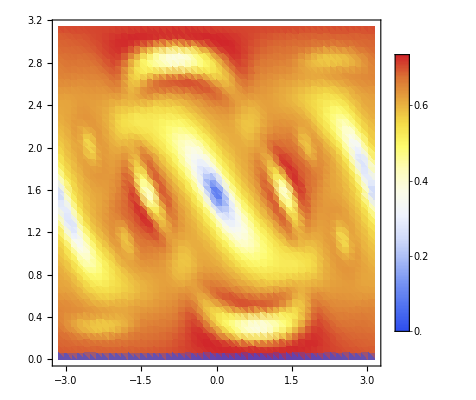
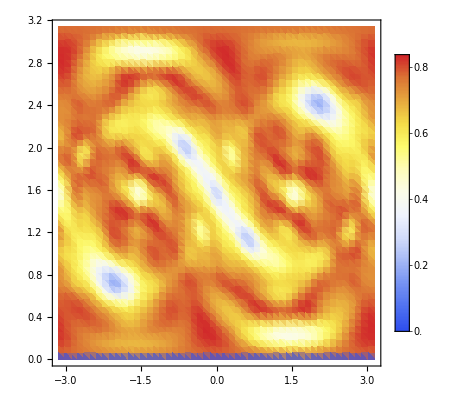
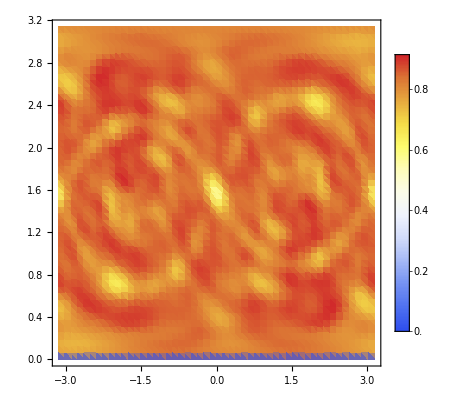

```mathematica
ListDensityPlot[#,Evaluate@DensityOptions]&/@{mtab,mtab1,mtab2}
```

## Heff

```mathematica
mtabEff=MultifractTabGenerator[Heff[100,100,4.0π/7,1.7],2,50];
```

```mathematica
mtab1Eff=MultifractTabGenerator[Heff[100,100,4.0π/7,3.],2,50];
```

```mathematica
mtab2Eff=MultifractTabGenerator[Heff[100,100,4.0π/7,7.],2,50];
```

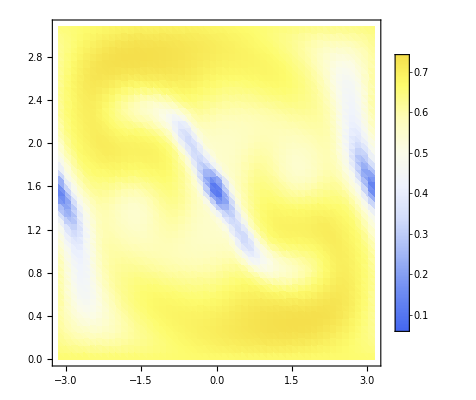
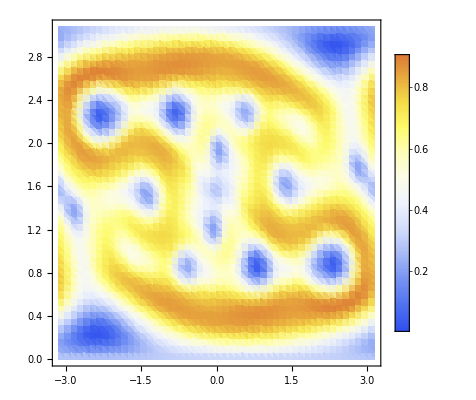
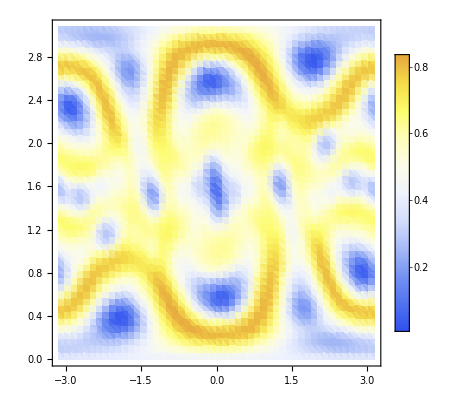

```mathematica
ListDensityPlot[#,Evaluate@DensityOptions]&/@{mtabEff,mtab1Eff,mtab2Eff}
```

```mathematica
mtabEff10=MultifractTabGenerator[Heff[100,10,4.0π/7,1.7],2,50];
```

```mathematica
mtab1Eff10=MultifractTabGenerator[Heff[100,10,4.0π/7,3.],2,50];
```

```mathematica
mtab2Eff10=MultifractTabGenerator[Heff[100,10,4.0π/7,7.],2,50];
```

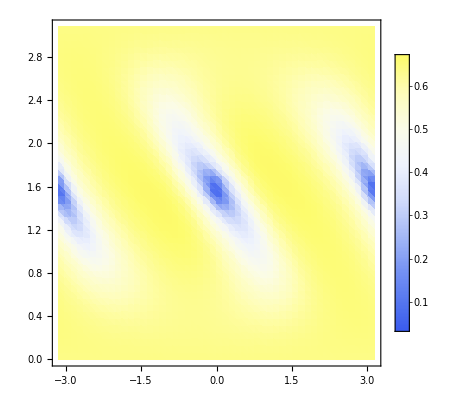
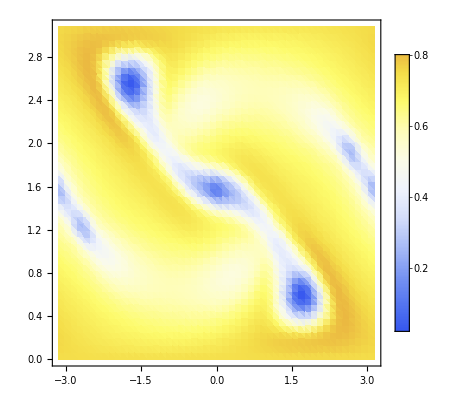
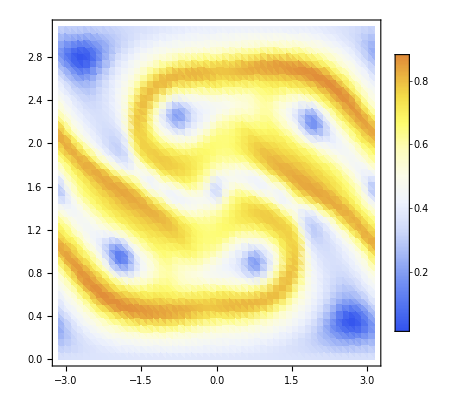

```mathematica
ListDensityPlot[#,Evaluate@DensityOptions]&/@{mtabEff10,mtab1Eff10,mtab2Eff10}
```

## Heff zeroth order H_0+H_z

```mathematica
mtab=MultifractTabGenerator[Heff0[100,4.0π/7,1.7],2,50];
```

```mathematica
mtab1=MultifractTabGenerator[Heff0[100,4.0π/7,3.],2,50];
```

```mathematica
mtab2=MultifractTabGenerator[Heff0[100,4.0π/7,7.],2,50];
```

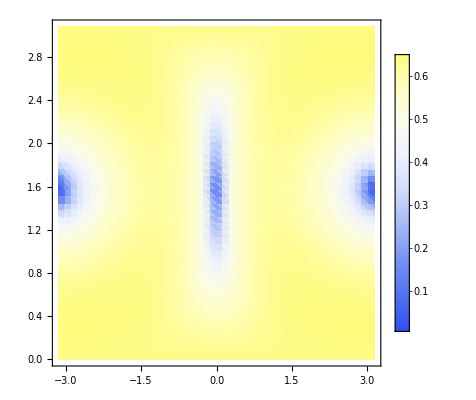
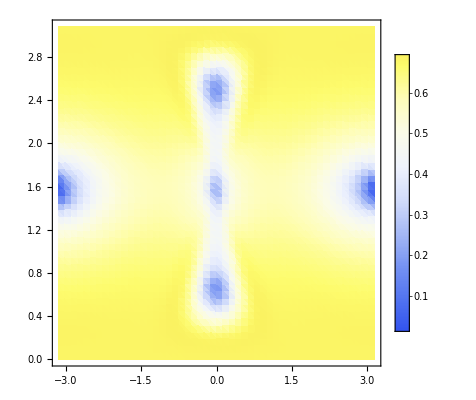
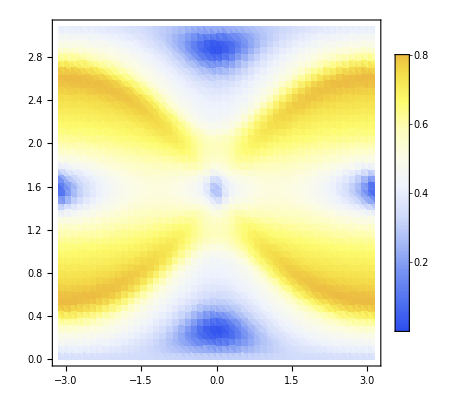

```mathematica
ListDensityPlot[#,Evaluate@DensityOptions]&/@{mtab,mtab1,mtab2}
```

## Sum of the multifract values - corresponds to λ dependence

### Floq

```mathematica
MakeTab[n_?IntegerQ,α_?NumericQ,κ_?NumericQ,res_?IntegerQ]:=MultifractTabGenerator[Floq[n,α,κ],2,res]
```

```mathematica
tab=ParallelTable[{κ,Total[MakeTab[30,4π/7,κ,20][[All,3]]]},{κ,0.01,7.,7./20}];
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

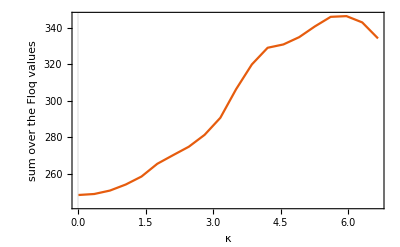

```mathematica
ListLinePlot[tab,FrameLabel->{"κ","sum over the Floq values"}]
```

### H_eff

```mathematica
MakeTabEff[n_?IntegerQ,bchOrder_?IntegerQ,α_?NumericQ,κ_?NumericQ,res_?IntegerQ]:=MultifractTabGenerator[Heff[n,bchOrder,α,κ],2,res]
```

```mathematica
tabEff=Quiet@ParallelTable[{κ,Total[MakeTabEff[30,10,4π/7,κ,20][[All,3]]]},{κ,0.01,7.,7./20}];
```

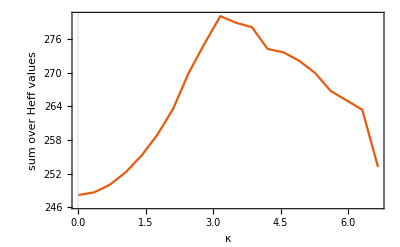

```mathematica
ListLinePlot[tabEff,FrameLabel->{"κ","sum over Heff values"}]
```

## Individual levels of Floq

```mathematica
ExtractK[tab_,k_]:=Transpose@{tab[[All,1]],tab[[All,2]],tab[[All,3]]}
```

```mathematica
mtabk=MultifractTabGeneratork[Floq[100,4.0π/7,1.7],1,50,#]&/@Range[10];
```

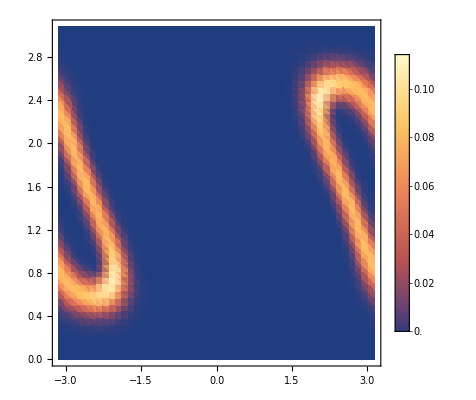
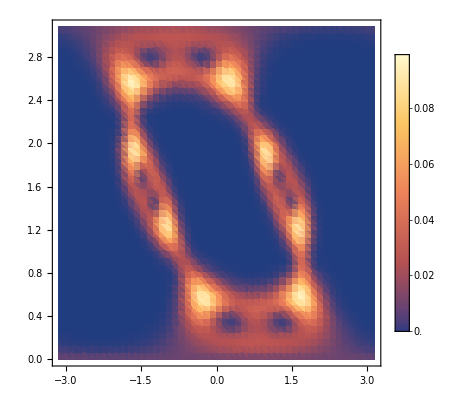
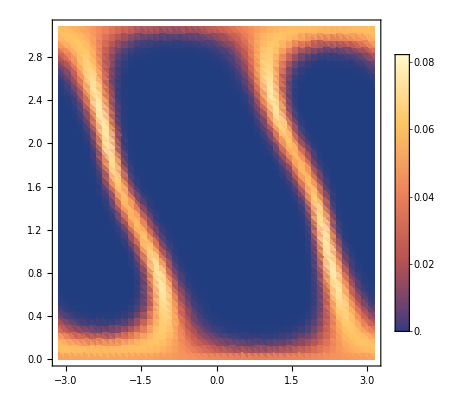
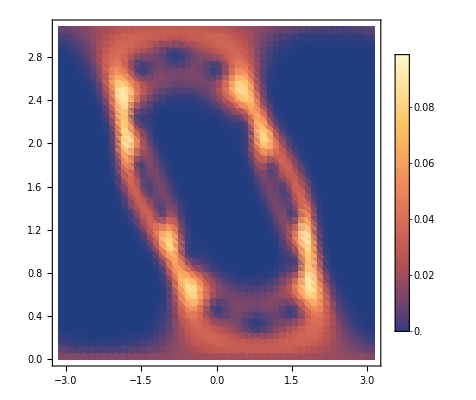
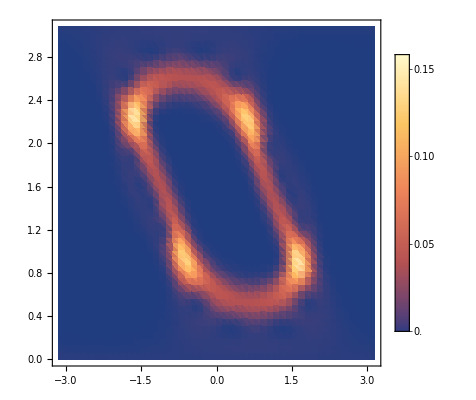
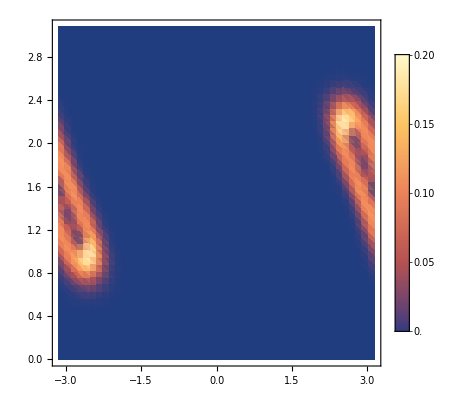
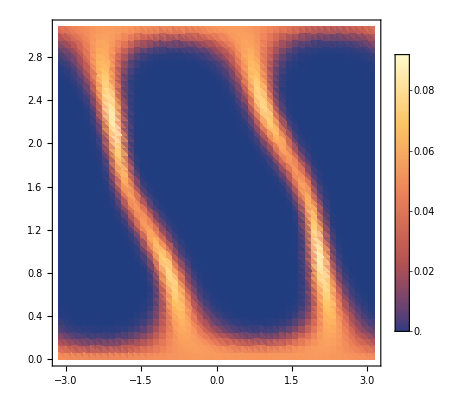
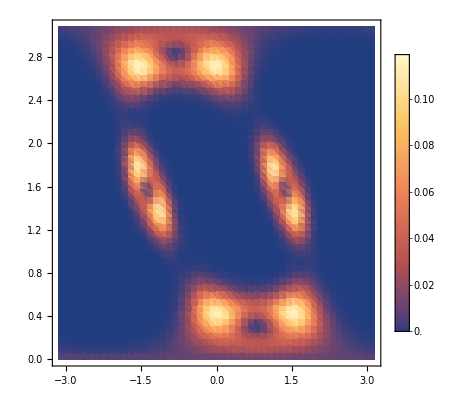

```mathematica
ListDensityPlot[ExtractK[#,1],PlotRange->All,PlotLegends->Automatic]&/@mtabk
```

```mathematica
MakeTabk[n_?IntegerQ,κ_?NumericQ,res_?IntegerQ]:=MultifractTabGeneratork[Floq[n,4.0π/7,κ],1,res,#]&/@Range[n+1];
```

```mathematica
IntegrateGridTabGeneratork[n_?IntegerQ,κ_?NumericQ,res_?IntegerQ]:=Module[{tab,levelsum},
tab=MakeTabk[n,κ,res];
levelsum=Table[Total@tab[[level,All,3]],{level,1,Length@tab}];(*sum over individual levels*)
Total@levelsum
]
```

```mathematica
tabsum=ParallelTable[{κ,IntegrateGridTabGeneratork[50,κ,20]},{κ,0.,6.,6./15}]
```

```mathematica
ListPlot[tabsum]
```